```mathematica
alphabeta[a_,b_,c_,d_,α_,β_]:={
-c/(a*α+b),
(d-a*β)/(a*α+b)
};
(* 
горната функция за x = α*y + β връща коефициенти Subscript[α, 1] и Subscript[β, 1], такива че,
y = Subscript[α, 1]*z + Subscript[β, 1], като имаме уравнението a*x + b*y + c*z = d
*)
TridiagonalSolve[A_,d_]:=Module[{n,a,b,c,α,β,x},
(* 
Аргументът A е обект, който задава i-тото уравнение в системата по следния начин: A[-1,i]*Subscript[x, i-1] + А[0,i]*Subscript[x, i] + A[1,i]*Subscript[x, i+1] = d[[i]] за i = 2,...,n-1,
където n е броят на променливите в системата; 
И съответно A[0,1]*Subscript[x, 1] + A[1,1]*Subscript[x, 2] = d[[1]] и A[-1,n]*Subscript[x, n-1] + A[0,n]*Subscript[x, n] = d[[n]];
Очаква се d да е вектор с размерност n
*)  
n=Length[d];
{a,b,c}=Table[If[i+j<1||i+j>n,0,A[j,i]],{j,-1,1},{i,1,n}];
α=Table[0,{n}];
β=Table[0,{n}];
α[[1]]=-c[[1]]/b[[1]];
β[[1]]=d[[1]]/b[[1]];
(* 
Долният ред изпълнява правият ход на метода на прогонката, тоест намираме коефициентите, със които Subscript[x, i] се изразява чрез Subscript[x, i+1] за i = 1,...,n-1 ;
И съответно на последна стъпка самата стойност на Subscript[x, n] ;
При намирането на тези коефициенти не правим проверки дали числото на което делим е 0, тъй като за системи произлизащи от задачата за интерполиране с кубични сплайн функции, поражда система от уравнения с тридиагонална матрица, с доминиращ главен диагонал, от което следва че това число винаги се получава положително
 *)
Do[{α[[k]],β[[k]]}=alphabeta[a[[k]],b[[k]],c[[k]],d[[k]],α[[k-1]],β[[k-1]]],{k,1,n}];
x=Table[0,{n}];
x[[n]]=β[[n]];
Do[x[[k]]=α[[k]]*x[[k+1]]+β[[k]],{k,n-1,1,-1}];
(* Горните два реда са обратният ход на метода на прогонката *)
x
];

GetCubicSplineDerivatives[f_,x_,n_]:=Module[{coeff,freecoeff,d},
Do[
coeff[-1,k]=1/(x[k]-x[k-1]);
coeff[0,k]=2*(1/(x[k+1]-x[k])+1/(x[k]-x[k-1]));
coeff[1,k]=1/(x[k+1]-x[k]);
freecoeff[k]=3*(f[x[k]]-f[x[k-1]])/(x[k]-x[k-1])^2+3*(f[x[k+1]]-f[x[k]])/(x[k+1]-x[k])^2,
(* 
задаваме коефициентите на всяко от n-1 на брой уравнения, с неизвестни Subscript[p, i]'(Subscript[x, i]), които поставят условието Subscript[p, i]''(Subscript[x, i+1])=Subscript[p, i+1]''(Subscript[x, i+1]) за полиномите Subscript[p, i](t), съвпадащи със сплайн функцията във всеки интервал от вида [Subscript[x, i],Subscript[x, i+1]] за i=0,...,n-1,
 *)
{k,1,n-1}
];
coeff[0,1]=N[coeff[0,1]];
freecoeff[1]=N[freecoeff[1]];(* този ред и горният са за да предизвикаме изчислението да стане числено, а не символно, за да намалим времето за изпълнението на програмата *)
d[0]=D[f[t],t]/.t->x[0];
d[n]=D[f[t],t]/.t->x[n];
(* тъй като в системата от уравнения, както е записана до момента, Subscript[p, 0]'(Subscript[x, 0]) и Subscript[p, n]'(Subscript[x, n]) участват като неизвестни, а по условие те трябва да съвпадат в съответните точки с прозводните на функцията, която интерполираме, то може да ги заместим в уравнението, в което участват, и да коригираме дясната му част.;
Не зануляваме съответния коефициент на променливата, тъй като той по подразбиране е извън матрицата на системата, и се игнорира от функцията TridiagonalSolve *)
freecoeff[1]=freecoeff[1]-d[0]*coeff[-1,1]; 
freecoeff[n-1]=freecoeff[n-1]-d[n]*coeff[1,n-1];
sol=TridiagonalSolve[coeff,Table[freecoeff[k],{k,n-1}]];
Print[MatrixForm[sol]];
Do[d[k]=sol[[k]],{k,1,n-1}];
d
];
```

(0.00169908
0.0182248
0.0469707
0.0469895
-8.67362×10^-18
-0.0469895
-0.0469707
-0.0182248
-0.00169908)

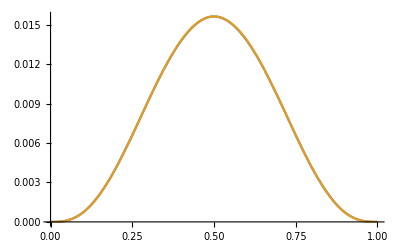

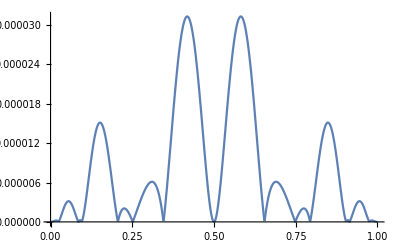

```mathematica
n=10;
Clear[f,x,a,b,d];
Do[x[k]=Sin[k*Pi/(2*n)]^2,{k,0,n}];
a=x[0];b=x[n];
f[t_]:=t^3*(1-t)^3;
d=GetCubicSplineDerivatives[f,x,n];
(* след като знаем какви производни в краищата трябва да имат полиномите, с които съвпада сплайн функцията във всеки от интервалите, зададен от съседни интерполационни възли, ги намираме чрез интерполационната формула на Ермит, като за стойности на полиномите в краищата избираме стойностите на функцията, която интерполираме *) 
Do[p[k_,t_]:=f[x[k]]+d[k]*(t-x[k])+((f[x[k+1]]-f[x[k]])/(x[k+1]-x[k])-d[k])/(x[k+1]-x[k])*(t-x[k])^2+(d[k+1]-2*(f[x[k+1]]-f[x[k]])/(x[k+1]-x[k])+d[k])/(x[k+1]-x[k])^2*(t-x[k])^2*(t-x[k+1]),
{k,0,n-1}
];
S[t_]:=Piecewise[Table[{p[k,t],t≥x[k]&&t≤x[k+1]},{k,0,n-1}]];
Plot[{S[t],f[t]},{t,a,b}]
Plot[Abs[f[t]-S[t]],{t,a,b}]
```